```mathematica
CountryData["UnitedStates","LaborForce"]
```

1.543×10^8 people

```mathematica
CountryData["UnitedStates","GDP"]/CountryData["UnitedStates","LaborForce"]
```

120703. $

```mathematica
CountryData[]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,North Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
Table[
{c,CountryData[c,"GDP"]/CountryData[c,"LaborForce"]},
{c,CountryData[]}
]
```

{{Afghanistan,1297.93 $},{Aland Islands,1},{Albania,10756. $},{Algeria,16805.7 $},{American Samoa,37322.7 $},{Andorra,67689.3 $},{Angola,13561. $},{Anguilla,34910.6 $},{Antigua and Barbuda,48671.5 $},{Argentina,33685. $},{Armenia,7138.62 $},{Aruba,62276.2 $},{Australia,107077. $},{Austria,107569. $},{Azerbaijan,6545.78 $},{Bahamas,64169.8 $},{Bahrain,57772.1 $},{Bangladesh,3124.68 $},{Barbados,25434.3 $},{Belarus,9736.54 $},{Belgium,93778.7 $},{Belize,14236.3 $},{Benin,2343.81 $},{Bermuda,145300. $},{Bhutan,(2.21264×10^9 $)/Missing[NotAvailable]},{Bolivia,7590.12 $},{Caribbean Netherlands,1},{Bosnia and Herzegovina,9076.91 $},{Botswana,22736.2 $},{Bouvet Island,1},{Brazil,19179.8 $},{British Indian Ocean Territory,1},{British Virgin Islands,71197.3 $},{Brunei,82055.3 $},{Bulgaria,19939.3 $},{Burkina Faso,1753.63 $},{Burundi,708.37 $},{Cambodia,2327.53 $},{Cameroon,4766.61 $},{Canada,83960.5 $},{Cape Verde,9316.79 $},{Cayman Islands,136760. $},{Central African Republic,911.799 $},{Chad,2236.38 $},{Chile,33993.1 $},{China,13865.5 $},{Christmas Island,1},{Cocos Keeling Islands,1},{Colombia,13261.2 $},{Comoros,2296.66 $},{Cook Islands,36328.4 $},{Costa Rica,24809.1 $},{Croatia,29298.1 $},{Cuba,17560. $},{Curacao,(2.871×10^9 $)/Missing[NotAvailable]},{Cyprus,50496.3 $},{Czech Republic,36437.5 $},{Democratic Republic of the Congo,1357.03 $},{Denmark,106562. $},{Djibouti,4910.44 $},{Dominica,23259.4 $},{Dominican Republic,17378.9 $},{East Timor,(1.78297×10^9 $)/Missing[NotAvailable]},{Ecuador,21253. $},{Egypt,13528.1 $},{El Salvador,9093.14 $},{Equatorial Guinea,(1.06848×10^10 $)/Missing[NotAvailable]},{Eritrea,(2.60774×10^9 $)/Missing[NotAvailable]},{Estonia,33676.6 $},{Ethiopia,1909.61 $},{Falkland Islands,60962.9 $},{Faroe Islands,107772. $},{Fiji,14040.7 $},{Finland,88236.4 $},{France,88146.4 $},{French Guiana,24764.5 $},{French Polynesia,29720.2 $},{French Southern And Antarctic lands,1},{Gabon,24464. $},{Gambia,1241.28 $},{Gaza Strip,2876.4 $},{Georgia,6205.45 $},{Germany,79766. $},{Ghana,4218.36 $},{Gibraltar,87155.2 $},{Greece,38849. $},{Greenland,69127.7 $},{Grenada,24969. $},{Guadeloupe,18354.2 $},{Guam,93360.2 $},{Guatemala,16953.5 $},{Guernsey,87130.6 $},{Guinea,1867.09 $},{Guinea-Bissau,1841.23 $},{Guyana,10489.4 $},{Haiti,2202.21 $},{Honduras,7193.89 $},{Hong Kong,84680. $},{Hungary,29956.3 $},{Iceland,108953. $},{India,4324.34 $},{Indonesia,8323.74 $},{Iran,17206.4 $},{Iraq,22156.2 $},{Ireland,136019. $},{Isle of Man,171137. $},{Israel,100127. $},{Italy,74030.8 $},{Ivory Coast,4951.35 $},{Jamaica,10779.8 $},{Japan,74288.1 $},{Jersey,95220.3 $},{Jordan,23934.8 $},{Kazakhstan,16319.3 $},{Kenya,4060.39 $},{Kiribati,23068.8 $},{Kosovo,12090.7 $},{Kuwait,53101.3 $},{Kyrgyzstan,2794.92 $},{Laos,7573.01 $},{Latvia,23112.1 $},{Lebanon,33490.1 $},{Lesotho,2681.16 $},{Liberia,(2.101×10^9 $)/Missing[NotAvailable]},{Libya,17776. $},{Liechtenstein,193871. $},{Lithuania,26480.1 $},{Luxembourg,284618. $},{Macau,132788. $},{North Macedonia,11783.3 $},{Madagascar,1052.31 $},{Malawi,945.37 $},{Malaysia,26739. $},{Maldives,31037.5 $},{Mali,4330.45 $},{Malta,63578.3 $},{Marshall Islands,13249.2 $},{Martinique,36871.6 $},{Mauritania,3595.83 $},{Mauritius,20836.4 $},{Mayotte,10475.8 $},{Mexico,23100.7 $},{Micronesia,20164.8 $},{Moldova,4936.82 $},{Monaco,138066. $},{Mongolia,10471.4 $},{Montenegro,16882. $},{Montserrat,12262.7 $},{Morocco,9176.82 $},{Mozambique,1141.44 $},{Myanmar,2159.3 $},{Namibia,15959. $},{Nauru,(6.34793×10^7 $)/Missing[NotAvailable]},{Nepal,1447.4 $},{Netherlands,100742. $},{New Caledonia,26143.7 $},{New Zealand,82208.5 $},{Nicaragua,5466.22 $},{Niger,1605.88 $},{Nigeria,7928.15 $},{Niue,15098. $},{Norfolk Island,Missing[NotAvailable] (0.000743494 /person)},{Northern Mariana Islands,32301.7 $},{North Korea,613.908 $},{Norway,143217. $},{Oman,68428.3 $},{Pakistan,5514.3 $},{Palau,31732.5 $},{Panama,39646.3 $},{Papua New Guinea,5554.61 $},{Paraguay,9659.76 $},{Peru,18843.9 $},{Philippines,8283.22 $},{Pitcairn Islands,Missing[NotAvailable] (0.0666667 /person)},{Poland,27711. $},{Portugal,36415.4 $},{Puerto Rico,69732.8 $},{Qatar,136239. $},{Republic of the Congo,(7.83351×10^9 $)/Missing[NotAvailable]},{Réunion,36454.8 $},{Romania,20127.9 $},{Russia,16950.6 $},{Rwanda,1883.95 $},{Saint Barthelemy,1},{Saint Helena, Ascension and Tristan da Cunha,7240.55 $},{Saint Kitts and Nevis,50074.6 $},{Saint Lucia,20916.9 $},{Saint Martin,1},{Saint Pierre and Miquelon,14000. $},{Saint Vincent and the Grenadines,13355.8 $},{Samoa,11865.9 $},{San Marino,70198.9 $},{São Tomé and Príncipe,6530.42 $},{Saudi Arabia,95910.7 $},{Senegal,2952.68 $},{Serbia,12934.8 $},{Seychelles,36080. $},{Sierra Leone,1693.06 $},{Singapore,101012. $},{Sint Maarten,(7.934×10^8 $)/Missing[NotAvailable]},{Slovakia,39826.4 $},{Slovenia,47562.3 $},{Solomon Islands,5936.42 $},{Somalia,1803.6 $},{South Africa,16608. $},{South Georgia and the South Sandwich Islands,1},{South Korea,57956.7 $},{South Sudan,(9.01522×10^9 $)/Missing[NotAvailable]},{Spain,54146.8 $},{Sri Lanka,10744.1 $},{Sudan,8018.82 $},{Suriname,19797.3 $},{Svalbard,1},{Eswatini,8125.46 $},{Sweden,105056. $},{Switzerland,165026. $},{Syria,7224.21 $},{Taiwan,39354.8 $},{Tajikistan,3310.31 $},{Tanzania,2247.87 $},{Thailand,10773.6 $},{Togo,1695.57 $},{Tokelau,3409.09 $},{Tonga,10049.1 $},{Trinidad and Tobago,44790.2 $},{Tunisia,11492.5 $},{Turkey,35898.2 $},{Turkmenistan,2678.01 $},{Turks and Caicos Islands,284806. $},{Tuvalu,9465.8 $},{Uganda,1656.05 $},{Ukraine,4324.08 $},{United Arab Emirates,106780. $},{United Kingdom,84787. $},{United States,120703. $},{United States Minor Outlying Islands,1},{United States Virgin Islands,75572.1 $},{Uruguay,31943.8 $},{Uzbekistan,4373.48 $},{Vanuatu,6673.88 $},{Vatican City,1},{Venezuela,38312.9 $},{Vietnam,4329.81 $},{Wallis and Futuna Islands,19329.9 $},{West Bank,22144. $},{Western Sahara,Missing[NotAvailable] (0.0000833333 /person)},{Yemen,5570.89 $},{Zambia,4023.68 $},{Zimbabwe,4114.87 $}}

```mathematica
TakeLargestBy[Out[4],Last,20]
```

Quantity::compatu: Incompatible units.

TakeLargestBy[{{Afghanistan,1297.93 $},{Aland Islands,1},{Albania,10756. $},{Algeria,16805.7 $},{American Samoa,37322.7 $},{Andorra,67689.3 $},{Angola,13561. $},{Anguilla,34910.6 $},{Antigua and Barbuda,48671.5 $},{Argentina,33685. $},{Armenia,7138.62 $},{Aruba,62276.2 $},{Australia,107077. $},{Austria,107569. $},{Azerbaijan,6545.78 $},{Bahamas,64169.8 $},{Bahrain,57772.1 $},{Bangladesh,3124.68 $},{Barbados,25434.3 $},{Belarus,9736.54 $},{Belgium,93778.7 $},{Belize,14236.3 $},{Benin,2343.81 $},{Bermuda,145300. $},{Bhutan,(2.21264×10^9 $)/Missing[NotAvailable]},{Bolivia,7590.12 $},{Caribbean Netherlands,1},{Bosnia and Herzegovina,9076.91 $},{Botswana,22736.2 $},{Bouvet Island,1},{Brazil,19179.8 $},{British Indian Ocean Territory,1},{British Virgin Islands,71197.3 $},{Brunei,82055.3 $},{Bulgaria,19939.3 $},{Burkina Faso,1753.63 $},{Burundi,708.37 $},{Cambodia,2327.53 $},{Cameroon,4766.61 $},{Canada,83960.5 $},{Cape Verde,9316.79 $},{Cayman Islands,136760. $},{Central African Republic,911.799 $},{Chad,2236.38 $},{Chile,33993.1 $},{China,13865.5 $},{Christmas Island,1},{Cocos Keeling Islands,1},{Colombia,13261.2 $},{Comoros,2296.66 $},{Cook Islands,36328.4 $},{Costa Rica,24809.1 $},{Croatia,29298.1 $},{Cuba,17560. $},{Curacao,(2.871×10^9 $)/Missing[NotAvailable]},{Cyprus,50496.3 $},{Czech Republic,36437.5 $},{Democratic Republic of the Congo,1357.03 $},{Denmark,106562. $},{Djibouti,4910.44 $},{Dominica,23259.4 $},{Dominican Republic,17378.9 $},{East Timor,(1.78297×10^9 $)/Missing[NotAvailable]},{Ecuador,21253. $},{Egypt,13528.1 $},{El Salvador,9093.14 $},{Equatorial Guinea,(1.06848×10^10 $)/Missing[NotAvailable]},{Eritrea,(2.60774×10^9 $)/Missing[NotAvailable]},{Estonia,33676.6 $},{Ethiopia,1909.61 $},{Falkland Islands,60962.9 $},{Faroe Islands,107772. $},{Fiji,14040.7 $},{Finland,88236.4 $},{France,88146.4 $},{French Guiana,24764.5 $},{French Polynesia,29720.2 $},{French Southern And Antarctic lands,1},{Gabon,24464. $},{Gambia,1241.28 $},{Gaza Strip,2876.4 $},{Georgia,6205.45 $},{Germany,79766. $},{Ghana,4218.36 $},{Gibraltar,87155.2 $},{Greece,38849. $},{Greenland,69127.7 $},{Grenada,24969. $},{Guadeloupe,18354.2 $},{Guam,93360.2 $},{Guatemala,16953.5 $},{Guernsey,87130.6 $},{Guinea,1867.09 $},{Guinea-Bissau,1841.23 $},{Guyana,10489.4 $},{Haiti,2202.21 $},{Honduras,7193.89 $},{Hong Kong,84680. $},{Hungary,29956.3 $},{Iceland,108953. $},{India,4324.34 $},{Indonesia,8323.74 $},{Iran,17206.4 $},{Iraq,22156.2 $},{Ireland,136019. $},{Isle of Man,171137. $},{Israel,100127. $},{Italy,74030.8 $},{Ivory Coast,4951.35 $},{Jamaica,10779.8 $},{Japan,74288.1 $},{Jersey,95220.3 $},{Jordan,23934.8 $},{Kazakhstan,16319.3 $},{Kenya,4060.39 $},{Kiribati,23068.8 $},{Kosovo,12090.7 $},{Kuwait,53101.3 $},{Kyrgyzstan,2794.92 $},{Laos,7573.01 $},{Latvia,23112.1 $},{Lebanon,33490.1 $},{Lesotho,2681.16 $},{Liberia,(2.101×10^9 $)/Missing[NotAvailable]},{Libya,17776. $},{Liechtenstein,193871. $},{Lithuania,26480.1 $},{Luxembourg,284618. $},{Macau,132788. $},{North Macedonia,11783.3 $},{Madagascar,1052.31 $},{Malawi,945.37 $},{Malaysia,26739. $},{Maldives,31037.5 $},{Mali,4330.45 $},{Malta,63578.3 $},{Marshall Islands,13249.2 $},{Martinique,36871.6 $},{Mauritania,3595.83 $},{Mauritius,20836.4 $},{Mayotte,10475.8 $},{Mexico,23100.7 $},{Micronesia,20164.8 $},{Moldova,4936.82 $},{Monaco,138066. $},{Mongolia,10471.4 $},{Montenegro,16882. $},{Montserrat,12262.7 $},{Morocco,9176.82 $},{Mozambique,1141.44 $},{Myanmar,2159.3 $},{Namibia,15959. $},{Nauru,(6.34793×10^7 $)/Missing[NotAvailable]},{Nepal,1447.4 $},{Netherlands,100742. $},{New Caledonia,26143.7 $},{New Zealand,82208.5 $},{Nicaragua,5466.22 $},{Niger,1605.88 $},{Nigeria,7928.15 $},{Niue,15098. $},{Norfolk Island,Missing[NotAvailable] (0.000743494 /person)},{Northern Mariana Islands,32301.7 $},{North Korea,613.908 $},{Norway,143217. $},{Oman,68428.3 $},{Pakistan,5514.3 $},{Palau,31732.5 $},{Panama,39646.3 $},{Papua New Guinea,5554.61 $},{Paraguay,9659.76 $},{Peru,18843.9 $},{Philippines,8283.22 $},{Pitcairn Islands,Missing[NotAvailable] (0.0666667 /person)},{Poland,27711. $},{Portugal,36415.4 $},{Puerto Rico,69732.8 $},{Qatar,136239. $},{Republic of the Congo,(7.83351×10^9 $)/Missing[NotAvailable]},{Réunion,36454.8 $},{Romania,20127.9 $},{Russia,16950.6 $},{Rwanda,1883.95 $},{Saint Barthelemy,1},{Saint Helena, Ascension and Tristan da Cunha,7240.55 $},{Saint Kitts and Nevis,50074.6 $},{Saint Lucia,20916.9 $},{Saint Martin,1},{Saint Pierre and Miquelon,14000. $},{Saint Vincent and the Grenadines,13355.8 $},{Samoa,11865.9 $},{San Marino,70198.9 $},{São Tomé and Príncipe,6530.42 $},{Saudi Arabia,95910.7 $},{Senegal,2952.68 $},{Serbia,12934.8 $},{Seychelles,36080. $},{Sierra Leone,1693.06 $},{Singapore,101012. $},{Sint Maarten,(7.934×10^8 $)/Missing[NotAvailable]},{Slovakia,39826.4 $},{Slovenia,47562.3 $},{Solomon Islands,5936.42 $},{Somalia,1803.6 $},{South Africa,16608. $},{South Georgia and the South Sandwich Islands,1},{South Korea,57956.7 $},{South Sudan,(9.01522×10^9 $)/Missing[NotAvailable]},{Spain,54146.8 $},{Sri Lanka,10744.1 $},{Sudan,8018.82 $},{Suriname,19797.3 $},{Svalbard,1},{Eswatini,8125.46 $},{Sweden,105056. $},{Switzerland,165026. $},{Syria,7224.21 $},{Taiwan,39354.8 $},{Tajikistan,3310.31 $},{Tanzania,2247.87 $},{Thailand,10773.6 $},{Togo,1695.57 $},{Tokelau,3409.09 $},{Tonga,10049.1 $},{Trinidad and Tobago,44790.2 $},{Tunisia,11492.5 $},{Turkey,35898.2 $},{Turkmenistan,2678.01 $},{Turks and Caicos Islands,284806. $},{Tuvalu,9465.8 $},{Uganda,1656.05 $},{Ukraine,4324.08 $},{United Arab Emirates,106780. $},{United Kingdom,84787. $},{United States,120703. $},{United States Minor Outlying Islands,1},{United States Virgin Islands,75572.1 $},{Uruguay,31943.8 $},{Uzbekistan,4373.48 $},{Vanuatu,6673.88 $},{Vatican City,1},{Venezuela,38312.9 $},{Vietnam,4329.81 $},{Wallis and Futuna Islands,19329.9 $},{West Bank,22144. $},{Western Sahara,Missing[NotAvailable] (0.0000833333 /person)},{Yemen,5570.89 $},{Zambia,4023.68 $},{Zimbabwe,4114.87 $}},Last,20]

```mathematica
TakeLargestBy[Out[4],Composition[QuantityMagnitude,Last],20]
```

TakeLargestBy::rvec2: Input … is not a real-valued vector.

TakeLargestBy[{{Afghanistan,1297.93 $},{Aland Islands,1},{Albania,10756. $},{Algeria,16805.7 $},{American Samoa,37322.7 $},{Andorra,67689.3 $},{Angola,13561. $},{Anguilla,34910.6 $},{Antigua and Barbuda,48671.5 $},{Argentina,33685. $},{Armenia,7138.62 $},{Aruba,62276.2 $},{Australia,107077. $},{Austria,107569. $},{Azerbaijan,6545.78 $},{Bahamas,64169.8 $},{Bahrain,57772.1 $},{Bangladesh,3124.68 $},{Barbados,25434.3 $},{Belarus,9736.54 $},{Belgium,93778.7 $},{Belize,14236.3 $},{Benin,2343.81 $},{Bermuda,145300. $},{Bhutan,(2.21264×10^9 $)/Missing[NotAvailable]},{Bolivia,7590.12 $},{Caribbean Netherlands,1},{Bosnia and Herzegovina,9076.91 $},{Botswana,22736.2 $},{Bouvet Island,1},{Brazil,19179.8 $},{British Indian Ocean Territory,1},{British Virgin Islands,71197.3 $},{Brunei,82055.3 $},{Bulgaria,19939.3 $},{Burkina Faso,1753.63 $},{Burundi,708.37 $},{Cambodia,2327.53 $},{Cameroon,4766.61 $},{Canada,83960.5 $},{Cape Verde,9316.79 $},{Cayman Islands,136760. $},{Central African Republic,911.799 $},{Chad,2236.38 $},{Chile,33993.1 $},{China,13865.5 $},{Christmas Island,1},{Cocos Keeling Islands,1},{Colombia,13261.2 $},{Comoros,2296.66 $},{Cook Islands,36328.4 $},{Costa Rica,24809.1 $},{Croatia,29298.1 $},{Cuba,17560. $},{Curacao,(2.871×10^9 $)/Missing[NotAvailable]},{Cyprus,50496.3 $},{Czech Republic,36437.5 $},{Democratic Republic of the Congo,1357.03 $},{Denmark,106562. $},{Djibouti,4910.44 $},{Dominica,23259.4 $},{Dominican Republic,17378.9 $},{East Timor,(1.78297×10^9 $)/Missing[NotAvailable]},{Ecuador,21253. $},{Egypt,13528.1 $},{El Salvador,9093.14 $},{Equatorial Guinea,(1.06848×10^10 $)/Missing[NotAvailable]},{Eritrea,(2.60774×10^9 $)/Missing[NotAvailable]},{Estonia,33676.6 $},{Ethiopia,1909.61 $},{Falkland Islands,60962.9 $},{Faroe Islands,107772. $},{Fiji,14040.7 $},{Finland,88236.4 $},{France,88146.4 $},{French Guiana,24764.5 $},{French Polynesia,29720.2 $},{French Southern And Antarctic lands,1},{Gabon,24464. $},{Gambia,1241.28 $},{Gaza Strip,2876.4 $},{Georgia,6205.45 $},{Germany,79766. $},{Ghana,4218.36 $},{Gibraltar,87155.2 $},{Greece,38849. $},{Greenland,69127.7 $},{Grenada,24969. $},{Guadeloupe,18354.2 $},{Guam,93360.2 $},{Guatemala,16953.5 $},{Guernsey,87130.6 $},{Guinea,1867.09 $},{Guinea-Bissau,1841.23 $},{Guyana,10489.4 $},{Haiti,2202.21 $},{Honduras,7193.89 $},{Hong Kong,84680. $},{Hungary,29956.3 $},{Iceland,108953. $},{India,4324.34 $},{Indonesia,8323.74 $},{Iran,17206.4 $},{Iraq,22156.2 $},{Ireland,136019. $},{Isle of Man,171137. $},{Israel,100127. $},{Italy,74030.8 $},{Ivory Coast,4951.35 $},{Jamaica,10779.8 $},{Japan,74288.1 $},{Jersey,95220.3 $},{Jordan,23934.8 $},{Kazakhstan,16319.3 $},{Kenya,4060.39 $},{Kiribati,23068.8 $},{Kosovo,12090.7 $},{Kuwait,53101.3 $},{Kyrgyzstan,2794.92 $},{Laos,7573.01 $},{Latvia,23112.1 $},{Lebanon,33490.1 $},{Lesotho,2681.16 $},{Liberia,(2.101×10^9 $)/Missing[NotAvailable]},{Libya,17776. $},{Liechtenstein,193871. $},{Lithuania,26480.1 $},{Luxembourg,284618. $},{Macau,132788. $},{North Macedonia,11783.3 $},{Madagascar,1052.31 $},{Malawi,945.37 $},{Malaysia,26739. $},{Maldives,31037.5 $},{Mali,4330.45 $},{Malta,63578.3 $},{Marshall Islands,13249.2 $},{Martinique,36871.6 $},{Mauritania,3595.83 $},{Mauritius,20836.4 $},{Mayotte,10475.8 $},{Mexico,23100.7 $},{Micronesia,20164.8 $},{Moldova,4936.82 $},{Monaco,138066. $},{Mongolia,10471.4 $},{Montenegro,16882. $},{Montserrat,12262.7 $},{Morocco,9176.82 $},{Mozambique,1141.44 $},{Myanmar,2159.3 $},{Namibia,15959. $},{Nauru,(6.34793×10^7 $)/Missing[NotAvailable]},{Nepal,1447.4 $},{Netherlands,100742. $},{New Caledonia,26143.7 $},{New Zealand,82208.5 $},{Nicaragua,5466.22 $},{Niger,1605.88 $},{Nigeria,7928.15 $},{Niue,15098. $},{Norfolk Island,Missing[NotAvailable] (0.000743494 /person)},{Northern Mariana Islands,32301.7 $},{North Korea,613.908 $},{Norway,143217. $},{Oman,68428.3 $},{Pakistan,5514.3 $},{Palau,31732.5 $},{Panama,39646.3 $},{Papua New Guinea,5554.61 $},{Paraguay,9659.76 $},{Peru,18843.9 $},{Philippines,8283.22 $},{Pitcairn Islands,Missing[NotAvailable] (0.0666667 /person)},{Poland,27711. $},{Portugal,36415.4 $},{Puerto Rico,69732.8 $},{Qatar,136239. $},{Republic of the Congo,(7.83351×10^9 $)/Missing[NotAvailable]},{Réunion,36454.8 $},{Romania,20127.9 $},{Russia,16950.6 $},{Rwanda,1883.95 $},{Saint Barthelemy,1},{Saint Helena, Ascension and Tristan da Cunha,7240.55 $},{Saint Kitts and Nevis,50074.6 $},{Saint Lucia,20916.9 $},{Saint Martin,1},{Saint Pierre and Miquelon,14000. $},{Saint Vincent and the Grenadines,13355.8 $},{Samoa,11865.9 $},{San Marino,70198.9 $},{São Tomé and Príncipe,6530.42 $},{Saudi Arabia,95910.7 $},{Senegal,2952.68 $},{Serbia,12934.8 $},{Seychelles,36080. $},{Sierra Leone,1693.06 $},{Singapore,101012. $},{Sint Maarten,(7.934×10^8 $)/Missing[NotAvailable]},{Slovakia,39826.4 $},{Slovenia,47562.3 $},{Solomon Islands,5936.42 $},{Somalia,1803.6 $},{South Africa,16608. $},{South Georgia and the South Sandwich Islands,1},{South Korea,57956.7 $},{South Sudan,(9.01522×10^9 $)/Missing[NotAvailable]},{Spain,54146.8 $},{Sri Lanka,10744.1 $},{Sudan,8018.82 $},{Suriname,19797.3 $},{Svalbard,1},{Eswatini,8125.46 $},{Sweden,105056. $},{Switzerland,165026. $},{Syria,7224.21 $},{Taiwan,39354.8 $},{Tajikistan,3310.31 $},{Tanzania,2247.87 $},{Thailand,10773.6 $},{Togo,1695.57 $},{Tokelau,3409.09 $},{Tonga,10049.1 $},{Trinidad and Tobago,44790.2 $},{Tunisia,11492.5 $},{Turkey,35898.2 $},{Turkmenistan,2678.01 $},{Turks and Caicos Islands,284806. $},{Tuvalu,9465.8 $},{Uganda,1656.05 $},{Ukraine,4324.08 $},{United Arab Emirates,106780. $},{United Kingdom,84787. $},{United States,120703. $},{United States Minor Outlying Islands,1},{United States Virgin Islands,75572.1 $},{Uruguay,31943.8 $},{Uzbekistan,4373.48 $},{Vanuatu,6673.88 $},{Vatican City,1},{Venezuela,38312.9 $},{Vietnam,4329.81 $},{Wallis and Futuna Islands,19329.9 $},{West Bank,22144. $},{Western Sahara,Missing[NotAvailable] (0.0000833333 /person)},{Yemen,5570.89 $},{Zambia,4023.68 $},{Zimbabwe,4114.87 $}},QuantityMagnitude@*Last,20]

```mathematica
Grid@
TakeLargestBy[
Table[
{c,CountryData[c,"GDP"]/CountryData[c,"LaborForce"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"GDP"],
Not@MissingQ@CountryData[#,"LaborForce"]
]&]}],Last,30]
```

Turks and Caicos Islands | 284806. $
Luxembourg | 284618. $
Liechtenstein | 193871. $
Isle of Man | 171137. $
Switzerland | 165026. $
Bermuda | 145300. $
Norway | 143217. $
Monaco | 138066. $
Cayman Islands | 136760. $
Qatar | 136239. $
Ireland | 136019. $
Macau | 132788. $
United States | 120703. $
Iceland | 108953. $
Faroe Islands | 107772. $
Austria | 107569. $
Australia | 107077. $
United Arab Emirates | 106780. $
Denmark | 106562. $
Sweden | 105056. $
Singapore | 101012. $
Netherlands | 100742. $
Israel | 100127. $
Saudi Arabia | 95910.7 $
Jersey | 95220.3 $
Belgium | 93778.7 $
Guam | 93360.2 $
Finland | 88236.4 $
France | 88146.4 $
Gibraltar | 87155.2 $

```mathematica
CountryData["UnitedStates","SectorLaborFractions"]
```

{Agriculture→0.006,Industry→0.226,Services→0.768}

```mathematica
Map[{First@#,CountryData["UnitedStates","LaborForce"]Last@#}&,CountryData["UnitedStates","SectorLaborFractions"]]
```

{{Agriculture,925800. people},{Industry,3.48718×10^7 people},{Services,1.18502×10^8 people}}

```mathematica
CountryData["Germany","ExportValue"]
```

1.59439×10^12 $

```mathematica
Grid@
TakeLargestBy[
Table[
{c,PercentForm@(CountryData[c,"ExportValue"]/CountryData[c,"GDP"])},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"GDP"],
Not@MissingQ@CountryData[#,"ExportValue"]
]&]}],Last,30]
```

TakeLargestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeLargestBy[{{Afghanistan,6.896%},{Albania,28.89%},{Algeria,23.27%},{American Samoa,65.05%},{Andorra,34.3%},{Angola,28.83%},{Anguilla,49.1%},{Antigua and Barbuda,42.4%},{Argentina,12.66%},{Armenia,33.06%},{Aruba,70.77%},{Australia,18.87%},{Austria,51.65%},{Azerbaijan,46.45%},{Bahamas,32.45%},{Bahrain,73.91%},{Bangladesh,16.65%},{Barbados,36.89%},{Belarus,62.7%},{Belgium,84.17%},{Belize,57.67%},{Benin,30.55%},{Bermuda,47.67%},{Bhutan,29.73%},{Bolivia,24.59%},{Bosnia and Herzegovina,35.41%},{Botswana,55.4%},{Brazil,12.49%},{British Virgin Islands,109.7%},{Brunei,33.88%},{Bulgaria,62.56%},{Burkina Faso,26.08%},{Burundi,6.241%},{Cambodia,61.28%},{Cameroon,17.17%},{Canada,31%},{Cape Verde,41.05%},{Cayman Islands,61.95%},{Central African Republic,12.72%},{Chad,29.97%},{Chile,28.46%},{China,19.64%},{Colombia,14.04%},{Comoros,17.3%},{Cook Islands,82.81%},{Costa Rica,35.52%},{Croatia,51.11%},{Cuba,17.15%},{Cyprus,61.26%},{Czech Republic,79.36%},{Democratic Republic of the Congo,27.76%},{Denmark,52.97%},{Djibouti,28.03%},{Dominica,37.53%},{Dominican Republic,25.17%},{East Timor,3.92%},{Ecuador,19.15%},{Egypt,10.46%},{El Salvador,24.86%},{Equatorial Guinea,52.5%},{Eritrea,14.38%},{Estonia,78.91%},{Ethiopia,8.008%},{Falkland Islands,118.9%},{Faroe Islands,50.64%},{Fiji,26.23%},{Finland,35.1%},{France,29.43%},{French Guiana,8.865%},{French Polynesia,4.897%},{Gabon,41.07%},{Gambia,24%},{Gaza Strip,44.14%},{Georgia,43.34%},{Germany,45.84%},{Ghana,40.74%},{Gibraltar,24.5%},{Greece,30.45%},{Greenland,32.05%},{Grenada,22.81%},{Guadeloupe,4.207%},{Guam,19.4%},{Guatemala,19.53%},{Guinea,18.52%},{Guinea-Bissau,28.59%},{Guyana,46.46%},{Haiti,20.59%},{Honduras,42.72%},{Hong Kong,194%},{Hungary,91.42%},{Iceland,49.1%},{India,19.17%},{Indonesia,19.08%},{Iran,22.4%},{Iraq,32.56%},{Ireland,115.7%},{Israel,32.1%},{Italy,29.84%},{Ivory Coast,32.39%},{Jamaica,31.07%},{Japan,16.14%},{Jordan,35.12%},{Kazakhstan,31.78%},{Kenya,14.57%},{Kiribati,10.69%},{Kosovo,22.49%},{Kuwait,48.23%},{Kyrgyzstan,36.82%},{Laos,29.34%},{Latvia,58.21%},{Lebanon,52.23%},{Lesotho,39.13%},{Liberia,21.42%},{Libya,28.95%},{Liechtenstein,44.82%},{Lithuania,74.35%},{Luxembourg,233.1%},{Macau,75.74%},{North Macedonia,49.24%},{Madagascar,32.47%},{Malawi,33.35%},{Malaysia,67.2%},{Maldives,78.07%},{Mali,20.44%},{Malta,140.8%},{Marshall Islands,27.54%},{Martinique,6.608%},{Mauritania,36.21%},{Mauritius,44.49%},{Mayotte,1.392%},{Mexico,38.12%},{Micronesia,26.62%},{Moldova,43.43%},{Monaco,30.11%},{Mongolia,50.67%},{Montenegro,40.29%},{Montserrat,35.72%},{Morocco,33.98%},{Mozambique,34.76%},{Myanmar,0.0737%},{Namibia,42.23%},{Nauru,18.23%},{Nepal,10.66%},{Netherlands,80.15%},{New Caledonia,14.91%},{New Zealand,26.39%},{Nicaragua,40.62%},{Niger,17.17%},{Nigeria,12.64%},{Niue,2.012%},{Northern Mariana Islands,73.59%},{North Korea,5.889%},{Norway,33.74%},{Oman,41.55%},{Pakistan,8.842%},{Palau,56.32%},{Panama,44.77%},{Papua New Guinea,14.02%},{Paraguay,42.12%},{Peru,22.43%},{Philippines,27.97%},{Poland,52.08%},{Portugal,40.22%},{Puerto Rico,75.55%},{Qatar,47.49%},{Republic of the Congo,57.08%},{Réunion,2.28%},{Romania,41.19%},{Russia,25.71%},{Rwanda,15.05%},{Saint Helena, Ascension and Tristan da Cunha,105.6%},{Saint Kitts and Nevis,44.25%},{Saint Lucia,39.5%},{Saint Pierre and Miquelon,11.39%},{Saint Vincent and the Grenadines,25.78%},{Samoa,29.34%},{San Marino,232.1%},{São Tomé and Príncipe,11.63%},{Saudi Arabia,30.67%},{Senegal,28.9%},{Serbia,50.18%},{Seychelles,82.82%},{Sierra Leone,23.12%},{Singapore,172.1%},{Slovakia,93.59%},{Slovenia,77.79%},{Solomon Islands,43.29%},{Somalia,14.86%},{South Africa,30.26%},{South Korea,42.24%},{South Sudan,9.777%},{Spain,32.93%},{Sri Lanka,21.44%},{Sudan,9.829%},{Suriname,49.79%},{Eswatini,49.52%},{Sweden,44.1%},{Switzerland,65.81%},{Syria,38.64%},{Taiwan,59.7%},{Tajikistan,11.87%},{Tanzania,17.6%},{Thailand,68.9%},{Togo,42.71%},{Tokelau,0%},{Tonga,21.31%},{Trinidad and Tobago,36.34%},{Tunisia,40.17%},{Turkey,21.91%},{Turkmenistan,71.2%},{Turks and Caicos Islands,62.04%},{Tuvalu,1.512%},{Uganda,18.69%},{Ukraine,49.29%},{United Arab Emirates,103.8%},{United Kingdom,27.78%},{United States,11.89%},{United States Virgin Islands,40.69%},{Uruguay,21.35%},{Uzbekistan,20.62%},{Vanuatu,50.54%},{Venezuela,16.69%},{Vietnam,92.41%},{Wallis and Futuna Islands,0.07908%},{West Bank,18.16%},{Yemen,2.497%},{Zambia,35.14%},{Zimbabwe,21.89%}},Last,30]]

```mathematica
DeleteMissing@EntityClass["Country",All]["GDPPerCapita"]
```

{}

```mathematica
CountryData["UnitedStates","GDPPerCapita"]
```

57466.8 $

```mathematica
EntityClass["Country",All]
```

countries

```mathematica
DeleteMissing@EntityClass["Country",All]["GDPPerCapita"]
```

{}

```mathematica
DeleteMissing[EntityClass["Country",All]["GDPPerCapita"]]
```

{}

```mathematica
DeleteMissing[EntityClass["Country",All]["GDPPerCapita"]]
```

{}

```mathematica
EntityClass["Country",All]["GDPPerCapita"]
```

{Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}],Missing[UnknownProperty,{Country,GDPPerCapita}]}

```mathematica
DeleteMissing@
Table[CountryData[c,"GDPPerCapita"],{c,CountryData[]}]
```

{561.779 $,4146.9 $,3843.75 $,11834.7 $,36988.6 $,3110.81 $,19291.2 $,14353.4 $,12449.2 $,3606.15 $,25353.8 $,49927.8 $,44176.5 $,3876.94 $,23124.4 $,22354.2 $,1358.78 $,16096.9 $,4989.25 $,41096.2 $,4810.57 $,789.44 $,85748.1 $,2804. $,3104.96 $,4708.72 $,6788.04 $,8649.95 $,53302.5 $,26938.5 $,7350.8 $,649.73 $,285.727 $,1269.91 $,1032.65 $,42157.9 $,2997.75 $,64104.8 $,382.213 $,664.296 $,13792.9 $,8123.18 $,5805.61 $,775.08 $,10788.6 $,11824.6 $,12090.7 $,7602.26 $,23324.2 $,18266.5 $,444.505 $,53417.7 $,1862.17 $,7144.45 $,6722.22 $,1405.39 $,5968.98 $,3514.49 $,4223.58 $,8333.24 $,544.462 $,17574.7 $,706.758 $,35400. $,54117.8 $,5153.35 $,43090.2 $,36855. $,8300. $,14530.2 $,7179.34 $,473.19 $,2900. $,3853.65 $,41936.1 $,1513.46 $,38200. $,18104. $,39569.1 $,9469.22 $,7900. $,35562.6 $,4146.74 $,44600. $,508.145 $,620.215 $,4456.55 $,739.595 $,2361.16 $,43681.1 $,12664.8 $,59976.9 $,1709.39 $,3570.29 $,5219.11 $,4609.6 $,61606.5 $,81672. $,37292.6 $,30527.3 $,1526.2 $,4868.25 $,38894.5 $,57000. $,4087.94 $,7510.08 $,1455.36 $,1449.06 $,3661.43 $,27359.2 $,1077.04 $,2353.15 $,14118.1 $,7914. $,998.134 $,455.371 $,4643.31 $,168146. $,14879.7 $,102831. $,73187. $,5237.15 $,401.319 $,300.795 $,9502.57 $,8601.63 $,780.507 $,25058.2 $,3448.54 $,14400. $,1077.56 $,9627.6 $,4900. $,8201.31 $,3068.51 $,1843.24 $,163352. $,3686.45 $,6701. $,8272.34 $,2832.43 $,382.069 $,1275.02 $,4140.46 $,2396.15 $,729.533 $,45294.8 $,12579.6 $,39426.6 $,2151.38 $,363.227 $,2177.99 $,5800. $,22572.4 $,555.367 $,70812.5 $,14982.4 $,1468.19 $,13626. $,13680.2 $,2500.09 $,4080.2 $,6045.65 $,2951.07 $,12372.4 $,19813.3 $,28703.7 $,59330.9 $,1528.24 $,14390. $,9474.13 $,8748.36 $,702.836 $,2500. $,16725.3 $,7744.45 $,7000. $,7030.06 $,4027.76 $,47908.6 $,1756.06 $,20028.6 $,958.074 $,5348.29 $,15075.7 $,496.049 $,52960.7 $,16496. $,21304.6 $,2005.48 $,434.209 $,5273.59 $,27538.8 $,758.721 $,26528.5 $,3835.39 $,2415.04 $,6484.43 $,2775.15 $,51599.9 $,78812.7 $,2079.99 $,18545.1 $,795.844 $,879.194 $,5907.91 $,578.462 $,1000. $,3688.87 $,15377.1 $,3688.65 $,10787.6 $,6389.33 $,29879.9 $,3083.62 $,615.309 $,2185.73 $,37622.2 $,39899.4 $,57466.8 $,36350.8 $,15220.6 $,2110.65 $,2860.57 $,15692.4 $,2185.69 $,3800. $,2943.4 $,2500. $,990.335 $,1178.39 $,1008.6 $}

```mathematica
Quantile[%20,0.5]
```

5968.98 $

```mathematica
Table[f[Out[20]],{f,Mean,Median,Variance,StandardDeviation,Skewness,Kurtosis}]
```

Table::itform: Argument {f,Mean,Median,Variance,StandardDeviation,Skewness,Kurtosis} at position 2 does not have the correct form for an iterator.

Table[f[%20],{f,Mean,Median,Variance,StandardDeviation,Skewness,Kurtosis}]

```mathematica
Grid@
Table[{f,f[Out[20]]},{f,{Mean,Median,Variance,StandardDeviation,Skewness,Kurtosis}}]
```

Mean | 15936.7 $
Median | 6007.32 $
Variance | 5.60095×10^8 $^2/(person^2 yr^2)
StandardDeviation | 23666.3 $
Skewness | 3.09151
Kurtosis | 16.4989

```mathematica
Histogram[Out[20],PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Histogram[Out[20],PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
RandomReal[{1,2}]
```

1.12882

```mathematica
RandomReal[{1,2},10]
```

{1.52095,1.36709,1.14469,1.59068,1.00446,1.40832,1.20869,1.12509,1.14272,1.03693}

```mathematica
GeometricMean@Out[27]
```

1.24051

```mathematica
Fold[f,a]
```

Fold::normal: Nonatomic expression expected at position 2 in Fold[f,a].

Fold[f,a]

```mathematica
Prepend[Out[27],100]
```

{100,1.52095,1.36709,1.14469,1.59068,1.00446,1.40832,1.20869,1.12509,1.14272,1.03693}

```mathematica
Fold[Times,Out[30]]
```

863.006

```mathematica
100(GeometricMean@Out[27])^10
```

863.006

```mathematica
PercentForm@(15/60)
```

1/4

```mathematica
PercentForm@((N@15)/60)
```

25%

```mathematica
PercentForm@((N@11)/38)
```

28.95%

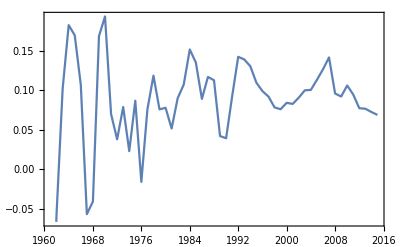

```mathematica
DateListPlot@CountryData["China",{"GDPRealGrowth",All}]
```

```mathematica
CountryData["China","GDPSectorFractions"]
```

{AgriculturalValueAdded→0.116132,ConstructionValueAdded→0.055798,IndustrialValueAdded→0.427557,MiscellaneousValueAdded→0.258816,TradeValueAdded→0.0828428,TransportationValueAdded→0.0588541}

```mathematica
CountryData["China",{"GDPSectorFractions",All}]
```

{{{1960,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1961,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1962,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1963,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1964,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1965,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1966,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1967,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1968,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1969,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{1970,1,1,0,0,0},{AgriculturalValueAdded→0.349868,ConstructionValueAdded→0.0370904,IndustrialValueAdded→0.365214,MiscellaneousValueAdded→0.125104,TradeValueAdded→0.0833177,TransportationValueAdded→0.0362684}},{{1971,1,1,0,0,0},{AgriculturalValueAdded→0.338392,ConstructionValueAdded→0.0393963,IndustrialValueAdded→0.379466,MiscellaneousValueAdded→0.122558,TradeValueAdded→0.0816226,TransportationValueAdded→0.0355306}},{{1972,1,1,0,0,0},{AgriculturalValueAdded→0.326519,ConstructionValueAdded→0.0372144,IndustrialValueAdded→0.390652,MiscellaneousValueAdded→0.124079,TradeValueAdded→0.0826313,TransportationValueAdded→0.0359708}},{{1973,1,1,0,0,0},{AgriculturalValueAdded→0.331454,ConstructionValueAdded→0.0367062,IndustrialValueAdded→0.391715,MiscellaneousValueAdded→0.12125,TradeValueAdded→0.0807535,TransportationValueAdded→0.035151}},{{1974,1,1,0,0,0},{AgriculturalValueAdded→0.336674,ConstructionValueAdded→0.0386113,IndustrialValueAdded→0.385971,MiscellaneousValueAdded→0.120519,TradeValueAdded→0.0802659,TransportationValueAdded→0.0349402}},{{1975,1,1,0,0,0},{AgriculturalValueAdded→0.322108,ConstructionValueAdded→0.0416564,IndustrialValueAdded→0.412883,MiscellaneousValueAdded→0.112744,TradeValueAdded→0.0750711,TransportationValueAdded→0.0326827}},{{1976,1,1,0,0,0},{AgriculturalValueAdded→0.326582,ConstructionValueAdded→0.044778,IndustrialValueAdded→0.406784,MiscellaneousValueAdded→0.111938,TradeValueAdded→0.0745699,TransportationValueAdded→0.0324531}},{{1977,1,1,0,0,0},{AgriculturalValueAdded→0.292539,ConstructionValueAdded→0.0424428,IndustrialValueAdded→0.426105,MiscellaneousValueAdded→0.120825,TradeValueAdded→0.0804675,TransportationValueAdded→0.0350321}},{{1978,1,1,0,0,0},{AgriculturalValueAdded→0.191224,ConstructionValueAdded→0.0379127,IndustrialValueAdded→0.440852,MiscellaneousValueAdded→0.122417,TradeValueAdded→0.0814578,TransportationValueAdded→0.0354756}},{{1979,1,1,0,0,0},{AgriculturalValueAdded→0.20952,ConstructionValueAdded→0.0353962,IndustrialValueAdded→0.43561,MiscellaneousValueAdded→0.110538,TradeValueAdded→0.0737409,TransportationValueAdded→0.0320586}},{{1980,1,1,0,0,0},{AgriculturalValueAdded→0.186725,ConstructionValueAdded→0.0430084,IndustrialValueAdded→0.439214,MiscellaneousValueAdded→0.110481,TradeValueAdded→0.0735178,TransportationValueAdded→0.0320402}},{{1981,1,1,0,0,0},{AgriculturalValueAdded→0.213738,ConstructionValueAdded→0.0423382,IndustrialValueAdded→0.418762,MiscellaneousValueAdded→0.112692,TradeValueAdded→0.0747937,TransportationValueAdded→0.0326075}},{{1982,1,1,0,0,0},{AgriculturalValueAdded→0.239051,ConstructionValueAdded→0.0414588,IndustrialValueAdded→0.406192,MiscellaneousValueAdded→0.111294,TradeValueAdded→0.0748134,TransportationValueAdded→0.0323548}},{{1983,1,1,0,0,0},{AgriculturalValueAdded→0.248938,ConstructionValueAdded→0.0453825,IndustrialValueAdded→0.398413,MiscellaneousValueAdded→0.115058,TradeValueAdded→0.0759877,TransportationValueAdded→0.0333622}},{{1984,1,1,0,0,0},{AgriculturalValueAdded→0.263886,ConstructionValueAdded→0.043937,IndustrialValueAdded→0.386928,MiscellaneousValueAdded→0.127351,TradeValueAdded→0.0838641,TransportationValueAdded→0.0365996}},{{1985,1,1,0,0,0},{AgriculturalValueAdded→0.268748,ConstructionValueAdded→0.0428398,IndustrialValueAdded→0.369646,MiscellaneousValueAdded→0.158112,TradeValueAdded→0.110406,TransportationValueAdded→0.0466255}},{{1986,1,1,0,0,0},{AgriculturalValueAdded→0.257385,ConstructionValueAdded→0.0473672,IndustrialValueAdded→0.37373,MiscellaneousValueAdded→0.166463,TradeValueAdded→0.1042,TransportationValueAdded→0.0479007}},{{1987,1,1,0,0,0},{AgriculturalValueAdded→0.212132,ConstructionValueAdded→0.0511444,IndustrialValueAdded→0.36832,MiscellaneousValueAdded→0.167245,TradeValueAdded→0.109188,TransportationValueAdded→0.0467877}},{{1988,1,1,0,0,0},{AgriculturalValueAdded→0.186218,ConstructionValueAdded→0.0497829,IndustrialValueAdded→0.371252,MiscellaneousValueAdded→0.165487,TradeValueAdded→0.121927,TransportationValueAdded→0.0454106}},{{1989,1,1,0,0,0},{AgriculturalValueAdded→0.180254,ConstructionValueAdded→0.0430092,IndustrialValueAdded→0.367231,MiscellaneousValueAdded→0.190711,TradeValueAdded→0.112042,TransportationValueAdded→0.0475909}},{{1990,1,1,0,0,0},{AgriculturalValueAdded→0.234545,ConstructionValueAdded→0.0425406,IndustrialValueAdded→0.354946,MiscellaneousValueAdded→0.193242,TradeValueAdded→0.0861651,TransportationValueAdded→0.0634924}},{{1991,1,1,0,0,0},{AgriculturalValueAdded→0.214342,ConstructionValueAdded→0.0429579,IndustrialValueAdded→0.357835,MiscellaneousValueAdded→0.19027,TradeValueAdded→0.108289,TransportationValueAdded→0.066684}},{{1992,1,1,0,0,0},{AgriculturalValueAdded→0.177855,ConstructionValueAdded→0.0485354,IndustrialValueAdded→0.368843,MiscellaneousValueAdded→0.195144,TradeValueAdded→0.115023,TransportationValueAdded→0.0644818}},{{1993,1,1,0,0,0},{AgriculturalValueAdded→0.135173,ConstructionValueAdded→0.0604487,IndustrialValueAdded→0.391272,MiscellaneousValueAdded→0.194872,TradeValueAdded→0.100263,TransportationValueAdded→0.0627927}},{{1994,1,1,0,0,0},{AgriculturalValueAdded→0.191836,ConstructionValueAdded→0.0590877,IndustrialValueAdded→0.397015,MiscellaneousValueAdded→0.1937,TradeValueAdded→0.0974046,TransportationValueAdded→0.0588851}},{{1995,1,1,0,0,0},{AgriculturalValueAdded→0.195,ConstructionValueAdded→0.0600002,IndustrialValueAdded→0.405984,MiscellaneousValueAdded→0.188439,TradeValueAdded→0.0949971,TransportationValueAdded→0.0536369}},{{1996,1,1,0,0,0},{AgriculturalValueAdded→0.194098,ConstructionValueAdded→0.0613611,IndustrialValueAdded→0.411847,MiscellaneousValueAdded→0.185542,TradeValueAdded→0.0923361,TransportationValueAdded→0.052897}},{{1997,1,1,0,0,0},{AgriculturalValueAdded→0.181247,ConstructionValueAdded→0.0587199,IndustrialValueAdded→0.418284,MiscellaneousValueAdded→0.193865,TradeValueAdded→0.0929295,TransportationValueAdded→0.0527102}},{{1998,1,1,0,0,0},{AgriculturalValueAdded→0.173854,ConstructionValueAdded→0.0592952,IndustrialValueAdded→0.404574,MiscellaneousValueAdded→0.208325,TradeValueAdded→0.096151,TransportationValueAdded→0.0554312}},{{1999,1,1,0,0,0},{AgriculturalValueAdded→0.163009,ConstructionValueAdded→0.0579491,IndustrialValueAdded→0.401799,MiscellaneousValueAdded→0.218313,TradeValueAdded→0.0984691,TransportationValueAdded→0.0579839}},{{2000,1,1,0,0,0},{AgriculturalValueAdded→0.149766,ConstructionValueAdded→0.0561948,IndustrialValueAdded→0.407381,MiscellaneousValueAdded→0.223662,TradeValueAdded→0.0979916,TransportationValueAdded→0.0626942}},{{2001,1,1,0,0,0},{AgriculturalValueAdded→0.143032,ConstructionValueAdded→0.0547283,IndustrialValueAdded→0.402093,MiscellaneousValueAdded→0.234657,TradeValueAdded→0.099529,TransportationValueAdded→0.0633882}},{{2002,1,1,0,0,0},{AgriculturalValueAdded→0.13636,ConstructionValueAdded→0.0544552,IndustrialValueAdded→0.399487,MiscellaneousValueAdded→0.243012,TradeValueAdded→0.100656,TransportationValueAdded→0.0631084}},{{2003,1,1,0,0,0},{AgriculturalValueAdded→0.12669,ConstructionValueAdded→0.0559219,IndustrialValueAdded→0.410191,MiscellaneousValueAdded→0.244416,TradeValueAdded→0.100634,TransportationValueAdded→0.0590753}},{{2004,1,1,0,0,0},{AgriculturalValueAdded→0.130554,ConstructionValueAdded→0.0542988,IndustrialValueAdded→0.407259,MiscellaneousValueAdded→0.251364,TradeValueAdded→0.0952401,TransportationValueAdded→0.0581091}},{{2005,1,1,0,0,0},{AgriculturalValueAdded→0.119021,ConstructionValueAdded→0.0553102,IndustrialValueAdded→0.421525,MiscellaneousValueAdded→0.267838,TradeValueAdded→0.0738167,TransportationValueAdded→0.0591412}},{{2006,1,1,0,0,0},{AgriculturalValueAdded→0.110026,ConstructionValueAdded→0.0559216,IndustrialValueAdded→0.430867,MiscellaneousValueAdded→0.251968,TradeValueAdded→0.0889111,TransportationValueAdded→0.0588946}},{{2007,1,1,0,0,0},{AgriculturalValueAdded→0.111362,ConstructionValueAdded→0.056162,IndustrialValueAdded→0.430278,MiscellaneousValueAdded→0.256641,TradeValueAdded→0.0858006,TransportationValueAdded→0.0585265}},{{2008,1,1,0,0,0},{AgriculturalValueAdded→0.112328,ConstructionValueAdded→0.055798,IndustrialValueAdded→0.427557,MiscellaneousValueAdded→0.258816,TradeValueAdded→0.0828428,TransportationValueAdded→0.0588541}},{{2009,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2010,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2011,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2012,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2013,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2014,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2015,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2016,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}}}

```mathematica
CountryData["China","GDPSectorFractions"]
```

{AgriculturalValueAdded→0.116132,ConstructionValueAdded→0.055798,IndustrialValueAdded→0.427557,MiscellaneousValueAdded→0.258816,TradeValueAdded→0.0828428,TransportationValueAdded→0.0588541}

```mathematica
CountryData["UnitedStates","GDPSectorFractions"]
```

{AgriculturalValueAdded→0.0107568,ConstructionValueAdded→0.047555,IndustrialValueAdded→0.169453,MiscellaneousValueAdded→0.56096,TradeValueAdded→0.151864,TransportationValueAdded→0.0594111}

```mathematica
Map[Last,Out[40]]
```

{0.0107568,0.047555,0.169453,0.56096,0.151864,0.0594111}

```mathematica
Total[{0.010756838045526653,0.04755499014466878,0.16945259890260495,0.5609602612358603,0.15186423508313204,0.05941107658834923}]
```

1.

```mathematica
CountryData["UnitedStates","AgriculturalValueAdded"]
```

183721000000 $

```mathematica
CountryData["UnitedStates","IndustrialValueAdded"]
```

2.38871×10^12 $

```mathematica
CountryData["UnitedStates","MiscellaneousValueAdded"]
```

7.90766×10^12 $

```mathematica
CountryData["UnitedStates","MiscellaneousValueAdded"]/CountryData["UnitedStates","GDP"]
```

0.424584

```mathematica
PercentForm@(CountryData["UnitedStates","MiscellaneousValueAdded"]/CountryData["UnitedStates","GDP"])
```

42.46%

```mathematica
Grid@
TakeLargestBy[
Table[
{c,PercentForm@(CountryData[c,"MiscellaneousValueAdded"]/CountryData[c,"GDP"])},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"MiscellaneousValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
```

TakeLargestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeLargestBy[{{Afghanistan,8.682%},{Albania,25.24%},{Algeria,13.41%},{Andorra,57.51%},{Angola,2.32%},{Anguilla,32.14%},{Antigua and Barbuda,26.38%},{Argentina,18.19%},{Armenia,19.01%},{Aruba,51.14%},{Australia,37.27%},{Austria,42.39%},{Azerbaijan,11.95%},{Bahamas,31.41%},{Bahrain,28.59%},{Bangladesh,9.034%},{Barbados,31.7%},{Belarus,26.88%},{Belgium,51.02%},{Belize,24.33%},{Benin,16.18%},{Bermuda,83.82%},{Bhutan,11.98%},{Bolivia,11.25%},{Bosnia and Herzegovina,34.1%},{Botswana,22.13%},{Brazil,28.59%},{British Virgin Islands,62.92%},{Brunei,19.98%},{Bulgaria,29.76%},{Burkina Faso,16.94%},{Burundi,10.6%},{Cambodia,10.22%},{Cameroon,12.24%},{Canada,42.34%},{Cape Verde,23.18%},{Cayman Islands,43.37%},{Central African Republic,14.23%},{Chad,11.33%},{Chile,21.54%},{China,9.698%},{Colombia,27.69%},{Comoros,13.25%},{Cook Islands,24.6%},{Costa Rica,19.5%},{Croatia,46.99%},{Cuba,28.77%},{Cyprus,56.46%},{Czech Republic,34.54%},{Democratic Republic of the Congo,3.142%},{Denmark,48.35%},{Djibouti,18.26%},{Dominica,17.27%},{Dominican Republic,18.55%},{East Timor,12.86%},{Ecuador,15.96%},{Egypt,14.08%},{El Salvador,23.49%},{Equatorial Guinea,4.207%},{Eritrea,14.27%},{Estonia,37.67%},{Ethiopia,6.3%},{Fiji,21.8%},{Finland,43.44%},{France,61.32%},{French Polynesia,72.76%},{Gabon,18.26%},{Gambia,15.01%},{Georgia,30.23%},{Germany,48.1%},{Ghana,7.574%},{Greece,71.92%},{Greenland,48.69%},{Grenada,23.83%},{Guatemala,16.95%},{Guinea,8.831%},{Guinea-Bissau,2.959%},{Guyana,7.565%},{Haiti,21.92%},{Honduras,22.66%},{Hong Kong,36.01%},{Hungary,46.14%},{Iceland,35.44%},{India,14.4%},{Indonesia,9.898%},{Iran,25.41%},{Iraq,3.102%},{Ireland,36.36%},{Israel,35.18%},{Italy,54.43%},{Ivory Coast,15%},{Jamaica,35.21%},{Japan,51.62%},{Jordan,20.24%},{Kazakhstan,27.48%},{Kenya,11.95%},{Kiribati,26.34%},{Kosovo,27.69%},{Kuwait,42.57%},{Kyrgyzstan,14.21%},{Laos,3.524%},{Latvia,48.82%},{Lebanon,25.76%},{Lesotho,26.7%},{Liberia,2.299%},{Libya,49.47%},{Liechtenstein,39.96%},{Lithuania,32.32%},{Luxembourg,51.34%},{Macau,26.87%},{North Macedonia,22.64%},{Madagascar,20.32%},{Malawi,20.38%},{Malaysia,17.62%},{Maldives,7.673%},{Mali,10.15%},{Malta,30.73%},{Marshall Islands,39.47%},{Mauritania,18.94%},{Mauritius,27.87%},{Mexico,33.51%},{Micronesia,32.79%},{Moldova,27.31%},{Monaco,55.2%},{Mongolia,8.743%},{Montenegro,37.55%},{Montserrat,54.54%},{Morocco,30.24%},{Mozambique,18.99%},{Myanmar,1.178%},{Namibia,29.33%},{Nauru,19.23%},{Nepal,15.75%},{Netherlands,51.64%},{New Caledonia,165.4%},{New Zealand,30.4%},{Nicaragua,17.04%},{Niger,12.1%},{Nigeria,3.941%},{North Korea,34.98%},{Norway,40.48%},{Oman,18.14%},{Pakistan,13.89%},{Palau,20.3%},{Panama,17.07%},{Papua New Guinea,5.045%},{Paraguay,12.17%},{Peru,19.21%},{Philippines,16.67%},{Poland,36.52%},{Portugal,50.68%},{Puerto Rico,34.04%},{Qatar,13.84%},{Republic of the Congo,17.94%},{Romania,28.84%},{Russia,32.01%},{Rwanda,13.81%},{Saint Kitts and Nevis,21.46%},{Saint Lucia,20.52%},{Saint Vincent and the Grenadines,22.1%},{Samoa,17.48%},{San Marino,52.47%},{São Tomé and Príncipe,8.495%},{Saudi Arabia,14.63%},{Senegal,22.34%},{Serbia,42.36%},{Seychelles,21.16%},{Sierra Leone,12.54%},{Singapore,25.88%},{Slovakia,32.21%},{Slovenia,44.12%},{Solomon Islands,18.03%},{Somalia,5.447%},{South Africa,35.52%},{South Korea,24.48%},{Spain,52.09%},{Sri Lanka,10.66%},{Sudan,11.37%},{Suriname,20.42%},{Eswatini,16.69%},{Sweden,41.67%},{Switzerland,33.9%},{Syria,23.65%},{Tajikistan,5.957%},{Tanzania,10%},{Thailand,12.1%},{Togo,12.2%},{Tonga,24.38%},{Trinidad and Tobago,17.75%},{Tunisia,24.08%},{Turkey,24.65%},{Turkmenistan,6.829%},{Turks and Caicos Islands,23.11%},{Tuvalu,46.88%},{Uganda,16.48%},{Ukraine,57.88%},{United Arab Emirates,20.57%},{United Kingdom,49.61%},{United States,42.46%},{Uruguay,21.17%},{Uzbekistan,7.051%},{Vanuatu,22.89%},{Venezuela,14.14%},{Vietnam,6.795%},{West Bank,18.16%},{Yemen,18.14%},{Zambia,15.54%},{Zimbabwe,8.164%}},Last,30]]

```mathematica
Grid@
TakeLargestBy[
Table[
{c,CountryData[c,"MiscellaneousValueAdded"]/CountryData[c,"GDP"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"MiscellaneousValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
```

New Caledonia | 1.6539
Bermuda | 0.838205
French Polynesia | 0.727582
Greece | 0.71922
British Virgin Islands | 0.629247
France | 0.613235
Ukraine | 0.578805
Andorra | 0.575088
Cyprus | 0.564604
Monaco | 0.551986
Montserrat | 0.545403
Italy | 0.544286
San Marino | 0.524708
Spain | 0.520909
Netherlands | 0.51645
Japan | 0.516163
Luxembourg | 0.51339
Aruba | 0.511388
Belgium | 0.510212
Portugal | 0.506814
United Kingdom | 0.496136
Libya | 0.494673
Latvia | 0.488168
Greenland | 0.486906
Denmark | 0.48352
Germany | 0.481037
Croatia | 0.469925
Tuvalu | 0.468807
Hungary | 0.461438
Slovenia | 0.441159

```mathematica
Grid@
Map[{First@#,PercentForm@Last@#}&,
TakeLargestBy[
Table[
{c,CountryData[c,"MiscellaneousValueAdded"]/CountryData[c,"GDP"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"MiscellaneousValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
]
```

New Caledonia | 165.4%
Bermuda | 83.82%
French Polynesia | 72.76%
Greece | 71.92%
British Virgin Islands | 62.92%
France | 61.32%
Ukraine | 57.88%
Andorra | 57.51%
Cyprus | 56.46%
Monaco | 55.2%
Montserrat | 54.54%
Italy | 54.43%
San Marino | 52.47%
Spain | 52.09%
Netherlands | 51.64%
Japan | 51.62%
Luxembourg | 51.34%
Aruba | 51.14%
Belgium | 51.02%
Portugal | 50.68%
United Kingdom | 49.61%
Libya | 49.47%
Latvia | 48.82%
Greenland | 48.69%
Denmark | 48.35%
Germany | 48.1%
Croatia | 46.99%
Tuvalu | 46.88%
Hungary | 46.14%
Slovenia | 44.12%

```mathematica
Grid@
Map[{First@#,PercentForm@Last@#}&,
TakeLargestBy[
Table[
{c,CountryData[c,"AgriculturalValueAdded"]/CountryData[c,"GDP"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"AgriculturalValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
]
```

Sierra Leone | 57.74%
Chad | 48.48%
Guinea-Bissau | 46.04%
Togo | 41.28%
Central African Republic | 40.46%
Niger | 38.78%
Sudan | 38.14%
Mali | 37.01%
Burundi | 36.36%
Ethiopia | 34.34%
Liberia | 34.2%
Kenya | 32.61%
Comoros | 30.81%
Burkina Faso | 30.43%
Rwanda | 29.53%
Nepal | 29.45%
Tanzania | 28.66%
Malawi | 26.08%
Vanuatu | 25.54%
Micronesia | 24.89%
Cambodia | 24.74%
Tajikistan | 24.74%
Haiti | 24.65%
Pakistan | 24.19%
Mauritania | 23.99%
Uganda | 23.98%
Myanmar | 23.61%
Benin | 23.17%
Kiribati | 22.87%
Mozambique | 22.55%

```mathematica
Select[{a,b,c},d==#&]
```

{}

```mathematica
Grid@
TakeLargestBy[
Table[
{c,CountryData[c,"AgriculturalValueAdded"]CountryData[c,"GDP"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"AgriculturalValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
```

China | 1.07315×10^25 $^(200%)/yr^(200%)
United States | 3.42171×10^24 $^(200%)/yr^(200%)
India | 8.00523×10^23 $^(200%)/yr^(200%)
Japan | 2.29267×10^23 $^(200%)/yr^(200%)
Brazil | 1.51977×10^23 $^(200%)/yr^(200%)
Indonesia | 1.08645×10^23 $^(200%)/yr^(200%)
France | 8.0165×10^22 $^(200%)/yr^(200%)
Russia | 7.03066×10^22 $^(200%)/yr^(200%)
Germany | 6.89954×10^22 $^(200%)/yr^(200%)
Italy | 6.49096×10^22 $^(200%)/yr^(200%)
Canada | 4.86322×10^22 $^(200%)/yr^(200%)
Turkey | 4.51947×10^22 $^(200%)/yr^(200%)
South Korea | 3.97308×10^22 $^(200%)/yr^(200%)
Mexico | 3.94826×10^22 $^(200%)/yr^(200%)
United Kingdom | 3.76752×10^22 $^(200%)/yr^(200%)
Australia | 3.5903×10^22 $^(200%)/yr^(200%)
Spain | 3.56217×10^22 $^(200%)/yr^(200%)
Nigeria | 3.43585×10^22 $^(200%)/yr^(200%)
Argentina | 1.90609×10^22 $^(200%)/yr^(200%)
Pakistan | 1.88206×10^22 $^(200%)/yr^(200%)
Iran | 1.69176×10^22 $^(200%)/yr^(200%)
Thailand | 1.38061×10^22 $^(200%)/yr^(200%)
Egypt | 1.31772×10^22 $^(200%)/yr^(200%)
Venezuela | 1.16958×10^22 $^(200%)/yr^(200%)
Saudi Arabia | 1.11967×10^22 $^(200%)/yr^(200%)
Netherlands | 9.56795×10^21 $^(200%)/yr^(200%)
Philippines | 8.97279×10^21 $^(200%)/yr^(200%)
Malaysia | 7.59795×10^21 $^(200%)/yr^(200%)
Bangladesh | 6.88579×10^21 $^(200%)/yr^(200%)
Vietnam | 6.7877×10^21 $^(200%)/yr^(200%)

```mathematica
CountryData["Mexico","PhoneLines"]
```

2.0539×10^7

```mathematica
CountryData["UnitedStates","CallingCode"]
```

1

```mathematica
CountryData["Mexico","CallingCode"]
```

52

```mathematica
CityData[{"Oslo", "Oslo", "Norway"}]
```

Oslo

```mathematica
CityData[{"Oslo", "Oslo", "Norway"}]["Population"]
```

658390 people

```mathematica
CityData[{"Oslo", "Oslo", "Norway"},"Population"]
```

623966 people

```mathematica
CityData[{"LosAngeles", "California", "UnitedStates"},"Population"]
```

3928864 people

```mathematica
Grid@
TakeLargestBy[
Table[
{c,CountryData[c,"IndustrialValueAdded"]CountryData[c,"GDP"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"IndustrialValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
```

United States | 4.44885×10^25 $^(200%)/yr^(200%)
China | 2.00928×10^25 $^(200%)/yr^(200%)
Japan | 5.72012×10^24 $^(200%)/yr^(200%)
Germany | 2.95596×10^24 $^(200%)/yr^(200%)
United Kingdom | 1.11877×10^24 $^(200%)/yr^(200%)
France | 8.71239×10^23 $^(200%)/yr^(200%)
Italy | 8.0184×10^23 $^(200%)/yr^(200%)
Brazil | 5.65566×10^23 $^(200%)/yr^(200%)
Russia | 5.58468×10^23 $^(200%)/yr^(200%)
India | 5.53789×10^23 $^(200%)/yr^(200%)
Canada | 4.96464×10^23 $^(200%)/yr^(200%)
South Korea | 3.54963×10^23 $^(200%)/yr^(200%)
Spain | 3.14831×10^23 $^(200%)/yr^(200%)
Mexico | 3.10503×10^23 $^(200%)/yr^(200%)
Australia | 2.38704×10^23 $^(200%)/yr^(200%)
Saudi Arabia | 2.00555×10^23 $^(200%)/yr^(200%)
Indonesia | 1.87221×10^23 $^(200%)/yr^(200%)
Turkey | 1.22565×10^23 $^(200%)/yr^(200%)
Netherlands | 1.18547×10^23 $^(200%)/yr^(200%)
Switzerland | 7.10671×10^22 $^(200%)/yr^(200%)
Venezuela | 6.97072×10^22 $^(200%)/yr^(200%)
Norway | 6.24563×10^22 $^(200%)/yr^(200%)
Iran | 5.59798×10^22 $^(200%)/yr^(200%)
Argentina | 5.11634×10^22 $^(200%)/yr^(200%)
United Arab Emirates | 5.03336×10^22 $^(200%)/yr^(200%)
Poland | 5.02928×10^22 $^(200%)/yr^(200%)
Sweden | 4.93282×10^22 $^(200%)/yr^(200%)
Thailand | 4.9191×10^22 $^(200%)/yr^(200%)
Belgium | 3.76311×10^22 $^(200%)/yr^(200%)
Nigeria | 3.47401×10^22 $^(200%)/yr^(200%)

```mathematica
Grid@
TakeLargestBy[
Table[
{c,CountryData[c,"IndustrialValueAdded"],CountryData[c,"GDP"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"IndustrialValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
```

United States | 2.38871×10^12 $ | 1.86245×10^13 $
China | 1.79414×10^12 $ | 1.11991×10^13 $
Japan | 1.15788×10^12 $ | 4.94016×10^12 $
Germany | 8.49951×10^11 $ | 3.4778×10^12 $
United Kingdom | 4.22512×10^11 $ | 2.6479×10^12 $
France | 3.53379×10^11 $ | 2.46545×10^12 $
India | 2.44629×10^11 $ | 2.26379×10^12 $
Italy | 4.31349×10^11 $ | 1.85891×10^12 $
Brazil | 3.1487×10^11 $ | 1.79619×10^12 $
Canada | 3.24537×10^11 $ | 1.52976×10^12 $
South Korea | 2.51524×10^11 $ | 1.41125×10^12 $
Russia | 4.35228×10^11 $ | 1.28316×10^12 $
Spain | 2.54459×10^11 $ | 1.23726×10^12 $
Australia | 1.98158×10^11 $ | 1.20462×10^12 $
Mexico | 2.96587×10^11 $ | 1.04692×10^12 $
Indonesia | 2.00825×10^11 $ | 9.32259×10^11 $
Turkey | 1.41905×10^11 $ | 8.63712×10^11 $
Netherlands | 1.52525×10^11 $ | 7.77228×10^11 $
Switzerland | 1.06253×10^11 $ | 6.68851×10^11 $
Saudi Arabia | 3.10246×10^11 $ | 6.46438×10^11 $
Argentina | 9.33545×10^10 $ | 5.48055×10^11 $
Sweden | 9.58836×10^10 $ | 5.1446×10^11 $
Venezuela | 1.44513×10^11 $ | 4.82359×10^11 $
Poland | 1.06696×10^11 $ | 4.71364×10^11 $
Belgium | 8.0416×10^10 $ | 4.67956×10^11 $
Iran | 1.33611×10^11 $ | 4.18977×10^11 $
Thailand | 1.20855×10^11 $ | 4.07026×10^11 $
Nigeria | 8.58517×10^10 $ | 4.04653×10^11 $
Austria | 8.84856×10^10 $ | 3.908×10^11 $
Norway | 1.68311×10^11 $ | 3.71076×10^11 $

```mathematica
n(1+.25)
```

1.25 n

```mathematica
1.25 n
```

```mathematica
1.25 n-n
```

0.25 n

```mathematica
100(1+.25)
```

125.

```mathematica
100(1+.25)-100
```

25.

```mathematica
(100+25)(1+.25)
```

156.25

```mathematica
25 1.25
```

31.25

```mathematica
156.25-31.25
```

125.

```mathematica
(100+25+(1+.25)
```

```mathematica
31.25`-25
```

0``-1.4948500216800935

```mathematica
31.25-25
```

6.25

```mathematica
(100+25+6.25)(1+.25)
```

164.063

```mathematica
100(1+.25)^3
```

195.313

```mathematica
100(1+.25)^2
```

156.25

```mathematica
Grid@
TakeLargestBy[
Table[
{c,CountryData[c,"IndustrialValueAdded"]},
{c,Select[
CountryData[],
And[
Not@MissingQ@CountryData[#,"IndustrialValueAdded"],
Not@MissingQ@CountryData[#,"GDP"]
]&]}],Last,30]
```

United States | 2.38871×10^12 $
China | 1.79414×10^12 $
Japan | 1.15788×10^12 $
Germany | 8.49951×10^11 $
Russia | 4.35228×10^11 $
Italy | 4.31349×10^11 $
United Kingdom | 4.22512×10^11 $
France | 3.53379×10^11 $
Canada | 3.24537×10^11 $
Brazil | 3.1487×10^11 $
Saudi Arabia | 3.10246×10^11 $
Mexico | 2.96587×10^11 $
Spain | 2.54459×10^11 $
South Korea | 2.51524×10^11 $
India | 2.44629×10^11 $
Indonesia | 2.00825×10^11 $
Australia | 1.98158×10^11 $
Norway | 1.68311×10^11 $
Netherlands | 1.52525×10^11 $
Venezuela | 1.44513×10^11 $
United Arab Emirates | 1.44328×10^11 $
Turkey | 1.41905×10^11 $
Iran | 1.33611×10^11 $
Thailand | 1.20855×10^11 $
Poland | 1.06696×10^11 $
Switzerland | 1.06253×10^11 $
Malaysia | 1.01391×10^11 $
Kuwait | 9.70499×10^10 $
Sweden | 9.58836×10^10 $
Argentina | 9.33545×10^10 $

```mathematica
CountryData["UnitedStates","GDPSectorFractions"]
```

{AgriculturalValueAdded→0.0107568,ConstructionValueAdded→0.047555,IndustrialValueAdded→0.169453,MiscellaneousValueAdded→0.56096,TradeValueAdded→0.151864,TransportationValueAdded→0.0594111}

```mathematica
Map[Last,Out[77]]
```

{0.0107568,0.047555,0.169453,0.56096,0.151864,0.0594111}

```mathematica
CountryData["Luxembourg","GDPSectorFractions"]
```

{AgriculturalValueAdded→0.0040915,ConstructionValueAdded→0.061957,IndustrialValueAdded→0.0971299,MiscellaneousValueAdded→0.622325,TradeValueAdded→0.118801,TransportationValueAdded→0.0956955}

```mathematica
CountryData["Luxembourg","LaborForce"]
```

206000. people

```mathematica
CountryData["Luxembourg","SectorLaborFractions"]
```

{Agriculture→0.022,Industry→0.172,Services→0.806}

```mathematica
{"Agriculture"->Quantity[206000., "People"]0.022,"Industry"->Quantity[206000., "People"]0.172,"Services"->Quantity[206000., "People"]0.806}
```

{Agriculture→4532. people,Industry→35432. people,Services→166036. people}

```mathematica
Table[{First@c,Last@c,CountryData["Luxembourg","SectorLaborFractions"]},{c,CountryData["Luxembourg","SectorLaborFractions"]}]
```

{{Agriculture,0.022,{Agriculture→0.022,Industry→0.172,Services→0.806}},{Industry,0.172,{Agriculture→0.022,Industry→0.172,Services→0.806}},{Services,0.806,{Agriculture→0.022,Industry→0.172,Services→0.806}}}

```mathematica
Table[{First@c,Last@c,CountryData["Luxembourg","LaborForce"]},{c,CountryData["Luxembourg","SectorLaborFractions"]}]
```

{{Agriculture,0.022,206000. people},{Industry,0.172,206000. people},{Services,0.806,206000. people}}

```mathematica
Table[{First@c,Last@c,Last@c CountryData["Luxembourg","LaborForce"]},{c,CountryData["Luxembourg","SectorLaborFractions"]}]
```

{{Agriculture,0.022,4532. people},{Industry,0.172,35432. people},{Services,0.806,166036. people}}

```mathematica
Table[{First@c,Last@c,Last@c CountryData["Liechtenstein","LaborForce"]},{c,CountryData["Liechtenstein","SectorLaborFractions"]}]
```

{{Agriculture,0.017,551.48 people},{Industry,0.434,14079. people},{Services,0.549,17809.6 people}}

```mathematica
Table[{First@c,Last@c,Last@c CountryData["Switzerland","LaborForce"]},{c,CountryData["Switzerland","SectorLaborFractions"]}]
```

{{Agriculture,0.039,158067. people},{Industry,0.228,924084. people},{Services,0.733,2.97085×10^6 people}}

```mathematica
Table[{First@c,Last@c,Last@c CountryData["Monaco","LaborForce"]},{c,CountryData["Monaco","SectorLaborFractions"]}]
```

Table::iterb: Iterator {c,Missing[NotAvailable]} does not have appropriate bounds.

Table[{First[c],Last[c],Last[c] CountryData[Monaco,LaborForce]},{c,Missing[NotAvailable]}]

```mathematica
Table[{First@c,Last@c,Last@c CountryData["India","LaborForce"]},{c,CountryData["India","SectorLaborFractions"]}]
```

{{Agriculture,0.6,3.141×10^8 people},{Industry,0.12,6.282×10^7 people},{Services,0.28,1.4658×10^8 people}}

```mathematica
DateListPlot@
CountryData["India",{"SectorLaborFractions",All}]
```

CountryData::notprop: {"SectorLaborFractions", All} is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

DateListPlot::ldata: CountryData[India,{SectorLaborFractions,All}] is not a valid dataset or list of datasets.

DateListPlot[CountryData[India,{SectorLaborFractions,All}]]

```mathematica
CountryData["India",{"SectorLaborFractions",All}]
```

CountryData::notprop: {"SectorLaborFractions", All} is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

CountryData[India,{SectorLaborFractions,All}]

```mathematica
DateListPlot@
CountryData["UnitedStates",{"SectorLaborFractions",All}]
```

CountryData::notprop: {"SectorLaborFractions", All} is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

DateListPlot::ldata: CountryData[UnitedStates,{SectorLaborFractions,All}] is not a valid dataset or list of datasets.

DateListPlot[CountryData[UnitedStates,{SectorLaborFractions,All}]]

```mathematica
DateListPlot@
CountryData["UnitedStates",{"GDPSectorFractions",All}]
```

DateListPlot::ldata: {{{1970,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0503801,IndustrialValueAdded→0.287324,Misc…dded→«19»,TradeValueAdded→0.189899,TransportationValueAdded→0.0705022}},«45»} is not a valid dataset or list of datasets.

DateListPlot[{{{1970,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0503801,IndustrialValueAdded→0.287324,MiscellaneousValueAdded→0.372496,TradeValueAdded→0.189899,TransportationValueAdded→0.0705022}},{{1971,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0509925,IndustrialValueAdded→0.280588,MiscellaneousValueAdded→0.377985,TradeValueAdded→0.18996,TransportationValueAdded→0.0712424}},{{1972,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0515854,IndustrialValueAdded→0.280066,MiscellaneousValueAdded→0.375356,TradeValueAdded→0.189908,TransportationValueAdded→0.0723469}},{{1973,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0513361,IndustrialValueAdded→0.278978,MiscellaneousValueAdded→0.36969,TradeValueAdded→0.188228,TransportationValueAdded→0.0714808}},{{1974,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0501632,IndustrialValueAdded→0.278167,MiscellaneousValueAdded→0.373854,TradeValueAdded→0.188805,TransportationValueAdded→0.0729004}},{{1975,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0473171,IndustrialValueAdded→0.276745,MiscellaneousValueAdded→0.380303,TradeValueAdded→0.191192,TransportationValueAdded→0.0701108}},{{1976,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0479818,IndustrialValueAdded→0.282465,MiscellaneousValueAdded→0.377602,TradeValueAdded→0.190092,TransportationValueAdded→0.0716918}},{{1977,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0473885,IndustrialValueAdded→0.287449,MiscellaneousValueAdded→0.378863,TradeValueAdded→0.187733,TransportationValueAdded→0.0712772}},{{1978,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0492644,IndustrialValueAdded→0.283577,MiscellaneousValueAdded→0.380104,TradeValueAdded→0.187709,TransportationValueAdded→0.0712753}},{{1979,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0499191,IndustrialValueAdded→0.280766,MiscellaneousValueAdded→0.382272,TradeValueAdded→0.186834,TransportationValueAdded→0.0704872}},{{1980,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0472304,IndustrialValueAdded→0.281244,MiscellaneousValueAdded→0.394894,TradeValueAdded→0.181964,TransportationValueAdded→0.0701628}},{{1981,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0423991,IndustrialValueAdded→0.289583,MiscellaneousValueAdded→0.393768,TradeValueAdded→0.178399,TransportationValueAdded→0.0693963}},{{1982,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0405955,IndustrialValueAdded→0.27843,MiscellaneousValueAdded→0.409946,TradeValueAdded→0.178236,TransportationValueAdded→0.0687087}},{{1983,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0404467,IndustrialValueAdded→0.26939,MiscellaneousValueAdded→0.421387,TradeValueAdded→0.180067,TransportationValueAdded→0.0704428}},{{1984,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0429379,IndustrialValueAdded→0.268258,MiscellaneousValueAdded→0.416332,TradeValueAdded→0.182175,TransportationValueAdded→0.0686507}},{{1985,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0449572,IndustrialValueAdded→0.256745,MiscellaneousValueAdded→0.426241,TradeValueAdded→0.183779,TransportationValueAdded→0.0679098}},{{1986,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0477627,IndustrialValueAdded→0.241142,MiscellaneousValueAdded→0.441608,TradeValueAdded→0.183096,TransportationValueAdded→0.0675808}},{{1987,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0467043,IndustrialValueAdded→0.239101,MiscellaneousValueAdded→0.449601,TradeValueAdded→0.177766,TransportationValueAdded→0.0678948}},{{1988,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0464724,IndustrialValueAdded→0.240219,MiscellaneousValueAdded→0.451186,TradeValueAdded→0.17817,TransportationValueAdded→0.0664956}},{{1989,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0453113,IndustrialValueAdded→0.234815,MiscellaneousValueAdded→0.458624,TradeValueAdded→0.177798,TransportationValueAdded→0.0643722}},{{1990,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0434615,IndustrialValueAdded→0.230309,MiscellaneousValueAdded→0.46857,TradeValueAdded→0.17444,TransportationValueAdded→0.0639428}},{{1991,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.039356,IndustrialValueAdded→0.22269,MiscellaneousValueAdded→0.479358,TradeValueAdded→0.175216,TransportationValueAdded→0.0656891}},{{1992,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0376819,IndustrialValueAdded→0.217153,MiscellaneousValueAdded→0.486504,TradeValueAdded→0.174648,TransportationValueAdded→0.06567}},{{1993,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.038183,IndustrialValueAdded→0.216074,MiscellaneousValueAdded→0.488157,TradeValueAdded→0.174485,TransportationValueAdded→0.066548}},{{1994,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0396835,IndustrialValueAdded→0.217776,MiscellaneousValueAdded→0.479762,TradeValueAdded→0.178121,TransportationValueAdded→0.067201}},{{1995,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0396823,IndustrialValueAdded→0.217576,MiscellaneousValueAdded→0.483077,TradeValueAdded→0.177005,TransportationValueAdded→0.0671442}},{{1996,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→0.0409823,IndustrialValueAdded→0.212075,MiscellaneousValueAdded→0.485454,TradeValueAdded→0.177879,TransportationValueAdded→0.0664473}},{{1997,1,1,0,0,0},{AgriculturalValueAdded→0.0139682,ConstructionValueAdded→0.04111,IndustrialValueAdded→0.207179,MiscellaneousValueAdded→0.491023,TradeValueAdded→0.179039,TransportationValueAdded→0.0658466}},{{1998,1,1,0,0,0},{AgriculturalValueAdded→0.0126851,ConstructionValueAdded→0.0430622,IndustrialValueAdded→0.19508,MiscellaneousValueAdded→0.527638,TradeValueAdded→0.157653,TransportationValueAdded→0.0647888}},{{1999,1,1,0,0,0},{AgriculturalValueAdded→0.012063,ConstructionValueAdded→0.044118,IndustrialValueAdded→0.19125,MiscellaneousValueAdded→0.531,TradeValueAdded→0.158113,TransportationValueAdded→0.0653415}},{{2000,1,1,0,0,0},{AgriculturalValueAdded→0.01211,ConstructionValueAdded→0.0446404,IndustrialValueAdded→0.189827,MiscellaneousValueAdded→0.535132,TradeValueAdded→0.155202,TransportationValueAdded→0.0651633}},{{2001,1,1,0,0,0},{AgriculturalValueAdded→0.0118941,ConstructionValueAdded→0.0465963,IndustrialValueAdded→0.176758,MiscellaneousValueAdded→0.54812,TradeValueAdded→0.155271,TransportationValueAdded→0.0635377}},{{2002,1,1,0,0,0},{AgriculturalValueAdded→0.0102137,ConstructionValueAdded→0.0462975,IndustrialValueAdded→0.171386,MiscellaneousValueAdded→0.556022,TradeValueAdded→0.154933,TransportationValueAdded→0.0622036}},{{2003,1,1,0,0,0},{AgriculturalValueAdded→0.0119248,ConstructionValueAdded→0.0454895,IndustrialValueAdded→0.169252,MiscellaneousValueAdded→0.560304,TradeValueAdded→0.154034,TransportationValueAdded→0.0604327}},{{2004,1,1,0,0,0},{AgriculturalValueAdded→0.013206,ConstructionValueAdded→0.0463589,IndustrialValueAdded→0.169401,MiscellaneousValueAdded→0.557854,TradeValueAdded→0.152807,TransportationValueAdded→0.0613533}},{{2005,1,1,0,0,0},{AgriculturalValueAdded→0.012073,ConstructionValueAdded→0.0489647,IndustrialValueAdded→0.168813,MiscellaneousValueAdded→0.559576,TradeValueAdded→0.152111,TransportationValueAdded→0.0597541}},{{2006,1,1,0,0,0},{AgriculturalValueAdded→0.0107952,ConstructionValueAdded→0.0492506,IndustrialValueAdded→0.171294,MiscellaneousValueAdded→0.559024,TradeValueAdded→0.152311,TransportationValueAdded→0.0588491}},{{2007,1,1,0,0,0},{AgriculturalValueAdded→0.01108,ConstructionValueAdded→0.0444496,IndustrialValueAdded→0.168251,MiscellaneousValueAdded→0.56428,TradeValueAdded→0.151171,TransportationValueAdded→0.05963}},{{2008,1,1,0,0,0},{AgriculturalValueAdded→0.0116499,ConstructionValueAdded→0.047555,IndustrialValueAdded→0.169453,MiscellaneousValueAdded→0.56096,TradeValueAdded→0.151864,TransportationValueAdded→0.0594111}},{{2009,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2010,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2011,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2012,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2013,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2014,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}},{{2015,1,1,0,0,0},{AgriculturalValueAdded→Missing[NotAvailable],ConstructionValueAdded→Missing[NotAvailable],IndustrialValueAdded→Missing[NotAvailable],MiscellaneousValueAdded→Missing[NotAvailable],TradeValueAdded→Missing[NotAvailable],TransportationValueAdded→Missing[NotAvailable]}}}]

```mathematica
With[{country=CountryData["Netherlands"]},
Table[
{First@c,Last@c,country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

{{Agriculture,0.02,9147479 people},{Industry,0.18,9147479 people},{Services,0.8,9147479 people}}

```mathematica
With[{country=CountryData["Denmark"]},
Table[
{First@c,Last@c,country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

{{Agriculture,0.03,3000535 people},{Industry,0.24,3000535 people},{Services,0.73,3000535 people}}

```mathematica
With[{country=CountryData["Finland"]},
Table[
{First@c,Last@c,country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

{{Agriculture,0.045,2698113 people},{Industry,0.256,2698113 people},{Services,0.699,2698113 people}}

```mathematica
With[{country=CountryData["Iceland"]},
Grid@
Table[
{First@c,Last@c,country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

Agriculture | 0.03 | 215769 people
Industry | 0.19 | 215769 people
Services | 0.78 | 215769 people

```mathematica
With[{country=Entity["Country","Sweden"]},
Grid@
Table[
{First@c,Last@c,country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

Agriculture | 0.011 | 5393425 people
Industry | 0.282 | 5393425 people
Services | 0.707 | 5393425 people

```mathematica
With[{country=Entity["Country","Sweden"]},
Grid@
Table[
{First@c,Last@c,Last@c country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

Agriculture | 0.011 | 59327.7 people
Industry | 0.282 | 1.52095×10^6 people
Services | 0.707 | 3.81315×10^6 people

```mathematica
With[{country=Entity["Country","Italy"]},
Grid@
Table[
{First@c,Last@c,Last@c country["LaborForce"]},
{c,country["SectorLaborFractions"]}]
]
```

Agriculture | 0.042 | 1.07457×10^6 people
Industry | 0.307 | 7.85458×10^6 people
Services | 0.651 | 1.66558×10^7 people